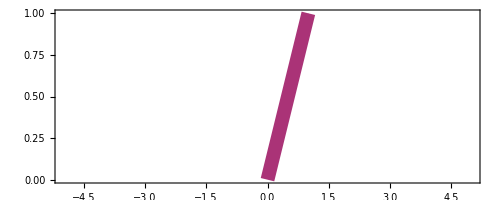

```mathematica
ClearAll[a];tk=0.025;ak=tk*4;
a[x_,y_,dx_,dy_,col_]:={Thickness[tk],Arrowheads[ak],col,Arrow[{{x,y},{x+dx,y+dy}}]};
Graphics[a[0,0,1,1,redpurple],PlotRange->{{-5,5},All},Frame->True]
```

```mathematica
xl=0.75;ay=0.5;yl=0;
tp[i_]=Join[a[#+i,ay,xl,yl,purpleblue],a[#-i,-ay,-xl,yl,redpurple]]&/@Table[i,{i,-10,10,1}];
```

```mathematica
he=1;anim=Animate[Graphics[{tp[u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0,-he},{0,he}}]}},PlotRange->{{-2,2},{-he,he}},Frame->False],{u,-5,5},AnimationRate->1,AppearanceElements->None,Bookmarks->{"start":>{u=-5},"stop":>{u=5}}]
```

```mathematica
anim=Table[Graphics[{tp[u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0,-he},{0,he}}]}},PlotRange->{{-2,2},{-he,he}},Frame->False],{u,-5,5,0.1}];
```

```mathematica
Export["pressureanimation.mp4",anim,"AnimationDuration"->10]
```

pressureanimation.mp4

```mathematica
xl=-0.75;ay=0.5;yl=0;
tp[i_]=Join[a[#+i,ay,xl,yl,purpleblue],a[#-i,-ay,-xl,yl,redpurple]]&/@Table[i,{i,-10,10,1}];
```

```mathematica
he=1;anim=Animate[Graphics[{tp[u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0,-he},{0,he}}]}},PlotRange->{{-2,2},{-he,he}},Frame->False],{u,-5,5},AnimationRate->1,AppearanceElements->None,Bookmarks->{"start":>{u=-5},"stop":>{u=5}}]
```

```mathematica
anim=Table[Graphics[{tp[u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0,-he},{0,he}}]}},PlotRange->{{-2,2},{-he,he}},Frame->False],{u,-5,5,0.1}];
```

```mathematica
Export["tensionanimation.mp4",anim,"AnimationDuration"->10]
```

tensionanimation.mp4

```mathematica
xl=0;ay=0.1;yl=0.7;
tp[i_]=Join[a[#+i,ay,xl,yl,purpleblue],a[#-i,-ay,-xl,-yl,redpurple]]&/@Table[i,{i,-10,10,1}];
```

```mathematica
1;anim=Animate[Graphics[{tp[u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0,-he},{0,he}}]}},PlotRange->{{-2,2},{-he,he}},Frame->False],{u,-5,5},AnimationRate->1,AppearanceElements->None,Bookmarks->{"start":>{u=-5},"stop":>{u=5}}]
```

```mathematica
anim=Table[Graphics[{tp[u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0,-he},{0,he}}]}},PlotRange->{{-2,2},{-he,he}},Frame->False],{u,-5,5,0.1}];
```

```mathematica
Export["shearanimation.mp4",anim,"AnimationDuration"->10]
```

shearanimation.mp4